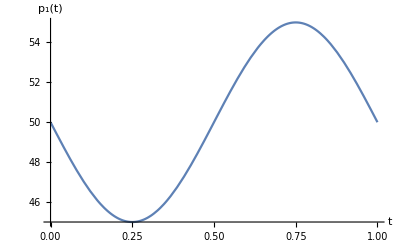

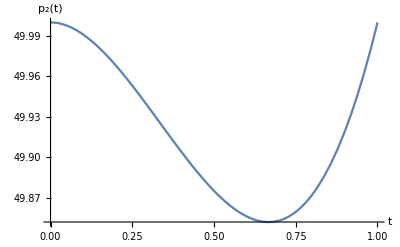

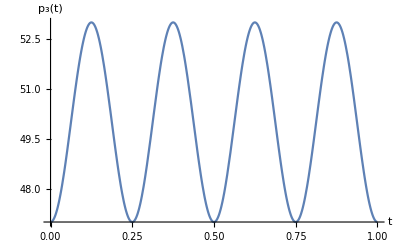

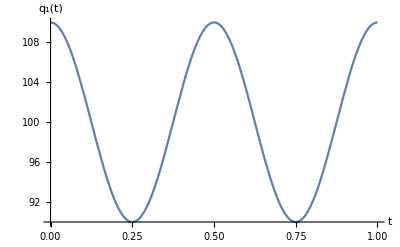

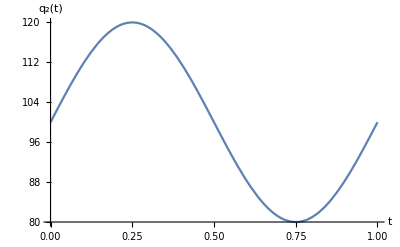

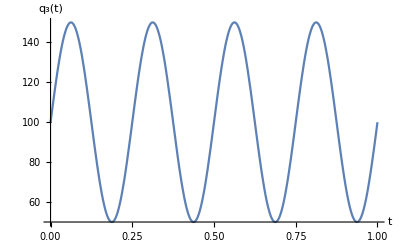

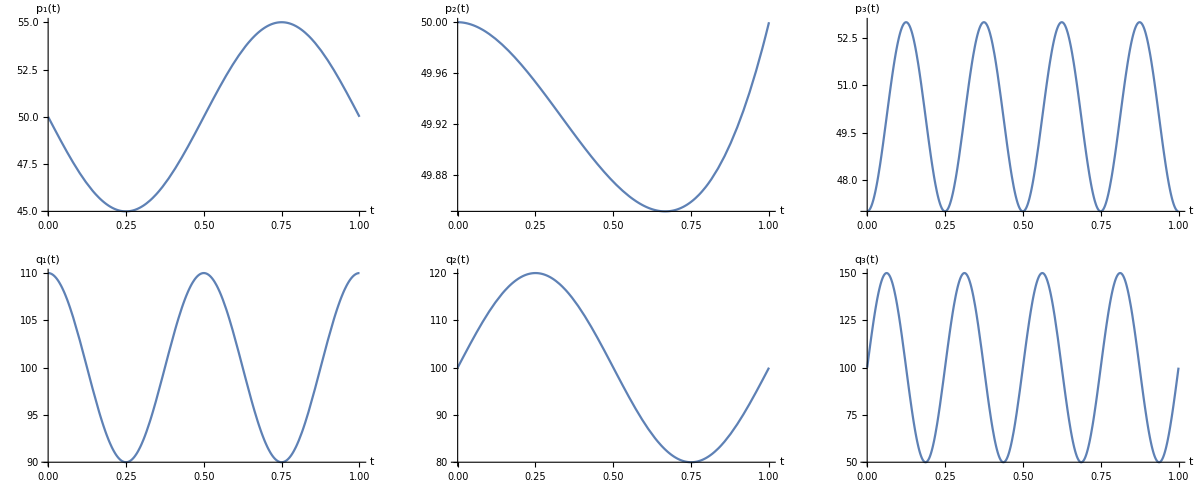

1.0893

```mathematica
p1[t_]:=50-5*Sin[2*π*t]
q1[t_]:=100+10*Cos[4*π*t];

p2[t_]:=50+t^3-t^2;
q2[t_]:=100+20*Sin[2*π*t];

p3[t_]:=50-3*Cos[8*π*t]
q3[t_]:=100+50*Sin[8*π*t];

f1=Plot[p1[t],{t,0,1},AxesLabel->{"t", "p_1(t)"}]
f2=Plot[p2[t],{t,0,1}, AxesLabel->{"t", "p_2(t)"}]
f3=Plot[p3[t],{t,0,1},AxesLabel->{"t", "p_3(t)"}]

f4=Plot[q1[t],{t,0,1},AxesLabel->{"t", "q_1(t)"}]
f5=Plot[q2[t],{t,0,1},AxesLabel->{"t", "q_2(t)"}]
f6=Plot[q3[t],{t,0,1},AxesLabel->{"t", "q_3(t)"}]

GraphicsGrid[{{f1,f2,f3},{f4,f5,f6}}]

f[t_]:=(q1[t]*(-10*π*Cos[2*π*t])+q2[t]*(3*t^2-2*t)+q3[t]*(Sin[8*π*t]*24*π))/(q1[t]*p1[t]+q2[t]*p2[t]+q3[t]*p3[t]
);

(*Divisia index - numerical approximation*)
Exp[∑_(k=0)^100000 0.00001*f[k*0.00001]]
```